```mathematica
(*Initial Condition for the Plate*)
Plot3D[-20*x(x-1.5)(x-3)y(y-1),{x,0,3},{y,0,1}]
```

-Graphics3D-

```mathematica
(*This is the system of the plate without any rods. This computation will be done to compare the heating/cooling at Pt1-Pt4 on the plate with and without the rods.*)
```

```mathematica
alpha1 = 0.05; kk = -20;
vvalsNoRod = NDSolveValue[{{D[v[x,y,t],t]==alpha1*(D[v[x,y,t],{x,2}]+D[v[x,y,t],{y,2}])},{v[x,y,0]==kk*x(x-1.5)(x-3)y(y-1)},{v[x,0,t]==0},{v[x,1,t]==0},{v[0,y,t]==0},{v[3,y,t]==0}},v,{x,0,3},{y,0,1},{t,0,20}]
```

InterpolatingFunction[{{0., 3.}, {0., 1.}, {0., 20.}}, <>]

```mathematica
(*This is Rod1*)
```

```mathematica
alpha2 = 0.2; 
uvals1 = NDSolveValue[{{D[u[y,t],t]==alpha2*D[u[y,t],{y,2}]},{u[y,0]==kk*y(y-1)},{u[0,t]==0},{u[1,t]==0}},u,{y,0,1},{t,0,20}]
```

InterpolatingFunction[{{0., 1.}, {0., 20.}}, <>]

```mathematica
(*This is used to demonstrate that since we have set alpha2 to be higher than alpha1, Rod1 cools down much faster than its part of the plate without the rod*)
```

```mathematica
Manipulate[Plot[{uvals1[y,t],vvalsNoRod[1,y,t],5},{y,0,1},PlotLegends -> {"Rod Temp","Plate Temp at Rod Location (no rod)","Max Temp"}],{t,0,10}]
```

```mathematica
(*This is Rod2*)
```

```mathematica
uvals2= NDSolveValue[{{D[u[y,t],t]==alpha2*D[u[y,t],{y,2}]},{u[y,0]==-kk*y(y-1)},{u[0,t]==0},{u[1,t]==0}},u,{y,0,1},{t,0,20}]
```

InterpolatingFunction[{{0., 1.}, {0., 20.}}, <>]

```mathematica
(*This is used to demonstrate that since we have set alpha2 to be higher than alpha1, Rod2 heats up much faster than its part of the plate without the rod*)
```

```mathematica
Manipulate[Plot[{uvals2[y,t],vvalsNoRod[2,y,t],-5},{y,0,1},PlotLegends -> {"Rod Temp","Plate Temp at Rod Location (no rod)","Min Temp"}],{t,0,10}]
```

```mathematica
(*This is solving for temperature in the left-most square in the plate with the rods, the region with rod 1 as the right boundary*)
```

```mathematica
vvalsRod1 = NDSolveValue[{{D[v[x,y,t],t]==alpha1*(D[v[x,y,t],{x,2}]+D[v[x,y,t],{y,2}])},{v[x,y,0]==kk*x(x-1.5)(x-3)y(y-1)},{v[x,0,t]==0},{v[x,1,t]==0},{v[0,y,t]==0},{v[1,y,t]==uvals1[y,t]}},v,{x,0,1},{y,0,1},{t,0,20}]
```

InterpolatingFunction[{{0., 1.}, {0., 1.}, {0., 20.}}, <>]

```mathematica
(*This is solving for temperature in the middle square in the plate with the rods, the region with rod 1 as the left boundary and rod 2 as the right boundary*)
```

```mathematica
vvalsRod2 = NDSolveValue[{{D[v[x,y,t],t]==alpha1*(D[v[x,y,t],{x,2}]+D[v[x,y,t],{y,2}])},{v[x,y,0]==kk*x(x-1.5)(x-3)y(y-1)},{v[x,0,t]==0},{v[x,1,t]==0},{v[2,y,t]==uvals2[y,t]},{v[1,y,t]==uvals1[y,t]}},v,{x,1,2},{y,0,1},{t,0,20}]
```

InterpolatingFunction[{{1., 2.}, {0., 1.}, {0., 20.}}, <>]

```mathematica
(*This is solving for temperature in the right-most square in the plate with the rods, the region with rod 2 as the left boundary*)
```

```mathematica
vvalsRod3 = NDSolveValue[{{D[v[x,y,t],t]==alpha1*(D[v[x,y,t],{x,2}]+D[v[x,y,t],{y,2}])},{v[x,y,0]==kk*x(x-1.5)(x-3)y(y-1)},{v[x,0,t]==0},{v[x,1,t]==0},{v[3,y,t]==0},{v[2,y,t]==uvals2[y,t]}},v,{x,2,3},{y,0,1},{t,0,20}]
```

InterpolatingFunction[{{2., 3.}, {0., 1.}, {0., 20.}}, <>]

```mathematica
(*Now we plot temperature over time for Pt1-4 with and without the cooling/heating effects of the rods*)
```

```mathematica
(*Plot For Pt1*)
```

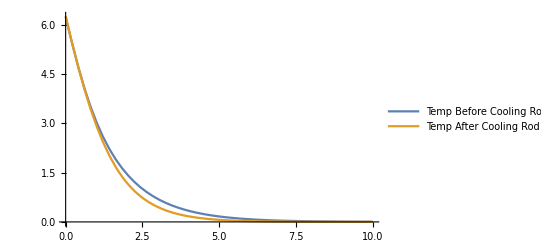

```mathematica
Plot[{vvalsNoRod[0.5,0.5,t],vvalsRod1[0.5,0.5,t]},{t,0,10},PlotLegends -> {"Temp Before Cooling Rod","Temp After Cooling Rod"}, PlotRange->All]
```

```mathematica
(*Plot For Pt2*)
```

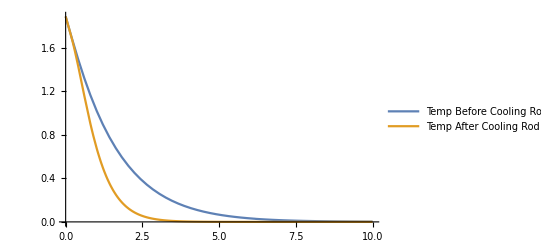

```mathematica
Plot[{vvalsNoRod[1.33,0.5,t],vvalsRod2[1.33,0.5,t]},{t,0,10},PlotLegends -> {"Temp Before Cooling Rod","Temp After Cooling Rod"}, PlotRange->All]
```

```mathematica
(*Plot For Pt3*)
```

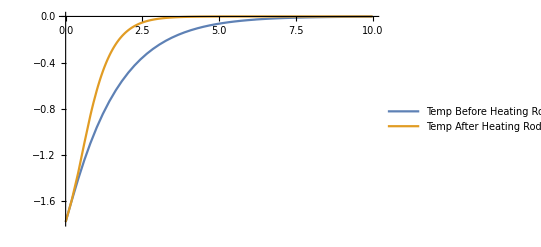

```mathematica
Plot[{vvalsNoRod[1.66,0.5,t],vvalsRod2[1.66,0.5,t]},{t,0,10},PlotLegends -> {"Temp Before Heating Rod","Temp After Heating Rod"}, PlotRange->All]
```

```mathematica
(*Plot For Pt4*)
```

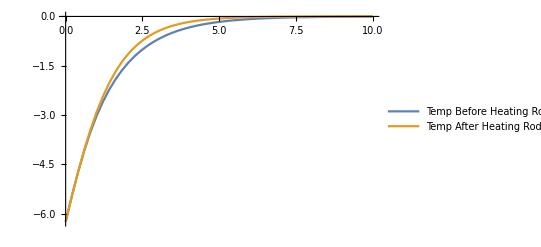

```mathematica
Plot[{vvalsNoRod[2.5,0.5,t],vvalsRod3[2.5,0.5,t]},{t,0,10},PlotLegends -> {"Temp Before Heating Rod","Temp After Heating Rod"}, PlotRange->All]
```